# Investigation of Bessel beams

Here,we will look intoBessel beamswhich are a specific type of nondiffractive beam. A Bessel beam is defined in terms of a Bessel function of the first kind,J_0(r, θ),and can be expressed in cylindrical coordinates as:

```mathematica
u[r_,θ_,k_,ω_,t_]:=BesselJ[0,r*k*Sin[θ]]*Cos[k*Cos[θ]-ω*t]
u[ρ, θ]
```

u[ρ,θ]

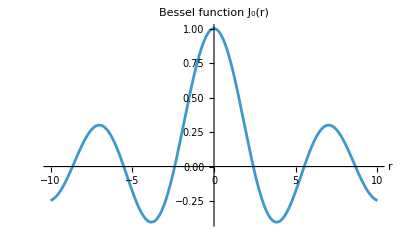

```mathematica
Plot[BesselJ[0, r], {r, -10, 10}, PlotLabel-> "Bessel function J_0(r)", AxesLabel->Automatic]
```

Since this is a function in cylindrical coordinates, we must be careful to plot it in a way that is slightly different from the standard method of plotting functions of the form f (x, y) . Below  we showcase how Mathematica can be able to plot cylindrical functions with a simple function :

```mathematica
f[r_, θ_, a_, b_] := a* θ (r^4 - b*r^2)
```

```mathematica
Manipulate[RevolutionPlot3D[f[r, θ, a, b], {r, 0, 10}, {θ, 0, 2π}], {a, 0.01, 1}, {b, 0, 5}]
```

We  will now showcase this in action to plot our Bessel beam :

```mathematica
Manipulate[RevolutionPlot3D[u[r, θ, k, ω, t], {r, 0, 10}, {θ, 0, 2π}], {k, 0.01, 1}, {ω, 0.01, 1}, {t, 0.01, 10}]
```

We can also use the typical Cartesian transformations r=√(x^2 + y^2), θ = arctan(y/x) to express u(r, θ)  in Cartesian coordinates, whereby we can see the spread of the beam as a function of distance:

```mathematica
u[Sqrt[x^2 + y^2], ArcTan[y/x], k, ω, t]
```

u_Cartesian[x,y,k,ω,t]

BesselJ[0,(k y √(x^2+y^2))/(x √(1+y^2/x^2))] Cos[k/(√(1+y^2/x^2))-t ω]

```mathematica
Manipulate[DensityPlot[u[Sqrt[x^2 + y^2], ArcTan[y/x], k, ω, t], {x, 0, 20}, {y, -10, 10}, PlotLegends->Automatic], {k, 0.01, 1}, {ω, 0.01, 1}, {t, 0.01, 10}]
```

This is effectively a 2D cross-section of the beam cone. As we can see, the beam does not diverge  - its central intensity is preserved for all time. We can see this even more clearly with a 3D density plot:

```mathematica
Manipulate[DensityPlot3D[u[Sqrt[x^2 + y^2 + t^2], ArcTan[y/Sqrt[x^2 + y^2]], k, ω, t], {x, 0, 20}, {y, -10, 10}, {t, 0.01, 30},PlotLegends->Automatic, AxesLabel->Automatic, PlotLabel->"Propagation of a Bessel beam through time"], {k, 0.01, 1}, {ω, 0.01, 1}]
```

```mathematica
Manipulate[ContourPlot3D[u[Sqrt[x^2 + y^2 + t^2], ArcTan[y/Sqrt[x^2 + y^2]], k, ω, t], {x, 0, 20}, {y, -10, 10}, {t, 0.01, 30},PlotLegends->Automatic, AxesLabel->Automatic, PlotLabel->"Isosurfaces of a Bessel beam through time"], {k, 0.01, 1}, {ω, 0.01, 1}]
```